```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
```

```mathematica
(*Soil Moisture PDF based on Numerical estimation of the normalization constant*)
Clear[pz,pzm,N1,N1A,χPDF,χIavgN,aλ,aPET, pzm, pz,pqm,PQm,σ2Qm,aλ,C1NFast]
(*Rainfall PDF, exponential and mixed exponential*)
pz[z_,γ_]:=γ ⅇ^(-γ z)UnitStep[z]
pzm[z_,ω_,γ1_,γ2_]:=(ω γ1 ⅇ^(-γ1 z)+(1-ω)γ2 ⅇ^(-γ2 z))UnitStep[z]
(*Soil Moisture (zero) top layer PDF *)
N1[DI_?NumericQ,γ_?NumericQ]:=N1[DI,γ]=1/NIntegrate[ⅇ^(-γ x0)x0^(γ/DI-1),{x0,0,1},AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
N1A[DI_,γ_]:=γ^(γ/DI)/(Gamma[γ/DI]-Gamma[γ/DI,γ])
χPDF[x0_,DI_,γ_]:=N1[DI,γ] ⅇ^(-γ x0)x0^(γ/DI-1)(*UnitStep[1-x0]UnitStep[x0]*)

(*Average based on the numerical PDF*)(*DI=(γ k)/λ*)
χIavgN[DI_?NumericQ,γ_?NumericQ]:=χIavgN[DI,γ]=NIntegrate[x0 χPDF[x0,DI,γ],{x0,0,1},AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
χIavgN1[DI_,γ_]:=UnitStep[χIavgN[DI,γ]-1]+UnitStep[1-χIavgN[DI,γ]]χIavgN[DI,γ]

(*frequency Adjustment*)
(*Based on probability of rainfall normalized exceeding average soil spare storage capacity*)
(*PET/(α λ) α/w PDF(x=1)*)
(*PET/(α λ) α/w PDF(x=1)*)
aλ[DI_,γ1_]:=DI/γ1 χPDF[1,DI,γ1]UnitStep[1-DI/γ1 χPDF[1,DI,γ1]]+UnitStep[DI/γ1 χPDF[1,DI,γ1]-1](*ⅇ^(-(1-χIavgN[DI,γ1,0,0])γ1)*)
aPET[DI_,γ1_]:=(1-χIavgN[DI,γ1])(*(1-(ⅇ^(10(DI-1))/(1+ⅇ^(10(DI-1)))))*)
(**)
ξ1=2; (*3.5 Lower Number Lowers Curve*)
ξ2=2; (*4.1 Higher Number Lowers Curve*)
ξ3=.55;(*1.35*)
ξ4=3.;
ϑ[LI_,γs_,β_]:=Max[-LI/(γs^(2(1-ξ1 β^2)))(ξ3+ξ4(β-β^2))+ⅇ^(-2(1-ξ2 β^2)LI/(γs^(1-.5 β^2))),0]
(*(DI aPET+BI)/aλ*)
(*First Moment--the Mean*)
CC1[LI_,γs_,β_,ϑ_]:=Gamma[(γs(1-ϑ))/(1-β ϑ)+1+γs/LI]/(Gamma[1+(γs(1-ϑ))/(1-β ϑ)]Gamma[γs/LI])(1/Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/LI ,(γs(1-ϑ))/(1-β ϑ)+1+γs/LI,β ϑ])
C1NFast[LI_?NumericQ,γ1_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=Module[{nodesU,weightsU,integrand,outerWeights,uu,n1,data},
(*Gauss-Legendre nodes and weights for[0,1]*)
n1=40;
data=GaussianQuadratureWeights[n1,-1,1];
nodesU=0.5*(data[[All,1]]+1); (* Shift from[-1,1] to[0,1]*)
weightsU=0.5*data[[All,2]];
(*Compute the integrand over the grid*)
integrand=MapThread[((1-#1 β ϑ)^(((1-β) γ1)/(β (1-β ϑ)))(1-#1)^((γ1 (1-ϑ))/(1-β ϑ)))/#1^(1-γ1/LI) &,{nodesU},1];
(*Final integral*)
1/Total[integrand*weightsU]
];
pχ[x_,LI_,γs_,β_,ϑ_]:=C1NFast[LI,γs,β,ϑ]((1-x β ϑ)^(((1-β) γs)/(β (1-β ϑ)))(1-x)^((γs (1-ϑ))/(1-β ϑ)))/x^(1-γs/LI)
(**)
χavg[LI_,γs_,β_,ϑ_]:=γs/(γs+LI(1+γs(1-ϑ)/(1-ϑ β)))(Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),1+γs/LI ,(γs(1-ϑ))/(1-β ϑ)+2+γs/LI,β ϑ]/Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/LI ,(γs(1-ϑ))/(1-β ϑ)+1+γs/LI,β ϑ])

χavgFast[LI_?NumericQ,γ1_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=Module[{nodesU,weightsU,N1,integrand,outerWeights,uu,n1,data},
N1=C1NFast[LI,γ1,β,ϑ];
n1=40;
(*Gauss-Legendre nodes and weights for[0,1]*)
data=GaussianQuadratureWeights[n1,-1,1];
nodesU=0.5*(data[[All,1]]+1); (* Shift from[-1,1] to[0,1]*)
weightsU=0.5*data[[All,2]];
(*Compute the integrand over the grid*)
integrand=MapThread[N1 #1((1-#1 β ϑ)^(((1-β) γ1)/(β (1-β ϑ)))(1-#1)^((γ1 (1-ϑ))/(1-β ϑ)))/#1^(1-γ1/LI) &,{nodesU},1];
(*Final integral*)
Total[integrand*weightsU]
];
(*Average of the square of soil moisture*)
χ2avg[LI_,γs_,β_,ϑ_]:=((γs(LI+γs))/((γs+LI(1+γs(1-ϑ)/(1-ϑ β))) (γs+LI(2+γs(1-ϑ)/(1-ϑ β)))))(Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),2+γs/LI ,(γs(1-ϑ))/(1-β ϑ)+3+γs/LI,β ϑ]/Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/LI ,(γs(1-ϑ))/(1-β ϑ)+1+γs/LI,β ϑ])
Budyko[DI_]:=(DI(1-ⅇ^-DI)Tanh[1/DI])^(.5)
(**)
Clear[pq,qavg,q2avg,pqm] 
pq[q_?NumericQ,LI_?NumericQ,γs_?NumericQ,β_?NumericQ]:=pq[q,LI,γs,β]=NIntegrate[(((2+q+u^2 β-u (2+β+q β)+√(4 q (-1+u) (-1+u β)+(q+u (-1-q+u) β)^2))/(2 √(4 q (-1+u) (-1+u β)+(q+u (-1-q+u) β)^2)))pz[1/(2 (-1+u β))(-q+u β+q u β-u^2 β-√(-4 (q-q u) (-1+u β)+(q-u β-q u β+u^2 β)^2)),γs]pχ[u,LI,γs ,β,ϑ[LI,γs,β]]),{u,0,1},Method->{Automatic,"SymbolicProcessing"->0} ]
(*Runoff Distribution (normalized) based on mixed exponential rainfall PDF*)
pqm[q_?NumericQ,LI_?NumericQ,γs_?NumericQ, β_?NumericQ,ω_?NumericQ,γ1_?NumericQ,γ2_?NumericQ]:=pqm[q,LI,γs,β,ω,γ1,γ2 ]=NIntegrate[(((2+q+u^2 β-u (2+β+q β)+√(4 q (-1+u) (-1+u β)+(q+u (-1-q+u) β)^2))/(2 √(4 q (-1+u) (-1+u β)+(q+u (-1-q+u) β)^2)))pzm[1/(2 (-1+u β))(-q+u β+q u β-u^2 β-√(-4 (q-q u) (-1+u β)+(q-u β-q u β+u^2 β)^2)),ω, γ1, γ2]pχ[u,LI,γs ,β,ϑ[LI,γs,β]])UnitStep[q],{u,0,1},Method->{Automatic,"SymbolicProcessing"->0},AccuracyGoal->3 ]
PQm[Q_?NumericQ,LI_?NumericQ,γs_?NumericQ, β_?NumericQ,w_?NumericQ,ω_?NumericQ,γ1_?NumericQ,γ2_?NumericQ]:=PQm[Q,LI,γs,β,w,ω,γ1,γ2]=NIntegrate[1/w pqm[Q1/w,LI,γs,β,ω,γ1,γ2 ]UnitStep[Q1],{Q1,0,Q},Method->{Automatic,"SymbolicProcessing"->0},AccuracyGoal->2]
(*q= α/w-(Qbmax+PET)/(α λa) α/w*)(*Q λa= λa α-Qbmax-PET*)
qavg[LI_,γs_,β_,ϑ_]:=1/γs(1-LI χavg[LI,γs,β,ϑ])
q2avg[LI_?NumericQ,γs_?NumericQ,β_?NumericQ]:=NIntegrate[q^2 pq[q,LI,γs,β],{q,0,∞},Method->{Automatic,"SymbolicProcessing"->0}]

σ2q [LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:= σ2q [LI,γs,β,ϑ]=NIntegrate[pq[q,LI,γs,β](q-qavg[LI,γs,β,ϑ])^2,{q,0,∞},Method->{Automatic,"SymbolicProcessing"->0}, AccuracyGoal->3]
σ2Q [LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ,w_?NumericQ]:= σ2Q [LI,γs,β,ϑ, w]=NIntegrate[1/w pq[Q/w,LI,γs,β](Q-w qavg[LI,γs,β,ϑ])^2,{Q,0,∞},Method->{Automatic,"SymbolicProcessing"->0}, AccuracyGoal->3]
(*Variance of runoff based on mixed exponential runoff PDF*)
σ2Qm [LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ,w_?NumericQ,ω_?NumericQ,γ1_?NumericQ,γ2_?NumericQ, DI_?NumericQ, γ0_?NumericQ]:= σ2Qm[LI,γs,β,ϑ, w,ω,γ1,γ2, DI, γ0]=NIntegrate[1/w pqm[Q/w,LI,γs,β,ω,γ1,γ2](Q-aλ[DI,γ0]w qavg[LI,γs,β,ϑ])^2,{Q,0,∞},Method->{Automatic,"SymbolicProcessing"->0}, AccuracyGoal->3]
(*4th Central Moment*)
μ4Qm [LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ,w_?NumericQ,ω_?NumericQ,γ1_?NumericQ,γ2_?NumericQ]:= μ4Qm[LI,γs,β,ϑ, w,ω,γ1,γ2]=NIntegrate[1/w pqm[Q/w,LI,γs,β,ω,γ1,γ2](Q-w qavg[LI,γs,β,ϑ])^4,{Q,0,∞},Method->{Automatic,"SymbolicProcessing"->0}, AccuracyGoal->3]
Clear[VarPDF,VarCDF,VarInverseCDF]
VarPDF[z_?NumericQ,n_?NumericQ,avg1_?NumericQ,avg2_?NumericQ]:=VarPDF[z,n,avg1,avg2]=NIntegrate[1/y PDF[GammaDistribution[n,avg1/n],z/y]PDF[GammaDistribution[n,avg2/n],y],{y,0,∞},AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]
VarCDF[z_?NumericQ,n_?NumericQ,avg1_?NumericQ,avg2_?NumericQ]:=VarCDF[z,n,avg1,avg2]=NIntegrate[VarPDF[z1,n,avg1,avg2],{z1,0,z},AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]
VarInverseCDF[P_?NumericQ,n_?NumericQ,avg1_?NumericQ,avg2_?NumericQ,guess_?NumericQ]:=VarInverseCDF[P,n,avg1,avg2,guess]=z/.FindRoot[VarCDF[z,n,avg1,avg2]==P,{z,guess,0,5}]
```

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"..","Data"}]];
hydroParametersImport=Import["USGS_gage_hydro_variables_jacksonville.csv"]; (*lwi-transition-zone jacksonville*)
(*Convert the data into an Association for easier access*)
columnNames=hydroParametersImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=hydroParametersImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
hydroParameters=AssociationThread[columnNames->#]&/@dataRows;

eventRunoffImport=Import["USGS_gage_event_runoff_jacksonville.csv"];
columnNames=eventRunoffImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=eventRunoffImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
eventRunoff=AssociationThread[columnNames->#]&/@dataRows;

eventRainfallImport=Import["USGS_gage_event_rainfall_jacksonville.csv"];
columnNames=eventRainfallImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=eventRainfallImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
eventRainfall=AssociationThread[columnNames->#]&/@dataRows;

hydroParametersYearImport=Import["USGS_gage_hydro_variables_w_year_jacksonville.csv"]; (*lwi-transition-zone jacksonville*)
(*Convert the data into an Association for easier access*)
columnNames=hydroParametersYearImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=hydroParametersYearImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
hydroParametersYear=AssociationThread[columnNames->#]&/@dataRows;

modelParametersImport=Import["Jacksonville_output.csv"]; 
(*Convert the data into an Association for easier access*)
columnNames=modelParametersImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=modelParametersImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
modelParameters=AssociationThread[columnNames->#]&/@dataRows;

Textsize = 14;
```

{ω→0.976083,α1→1.81075,α2→6.86594}

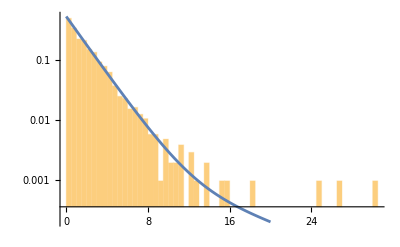

0.809327

0.427729

0.329775

1.27201

USGS site 2231342

1.81075

6.86594

1.93166

107.084

0.1

0.00372502

0.140005

0.0556243

```mathematica
site = 8;(*25, 35*)
eventRunoffsite = DeleteCases[eventRunoff[[All,site+1]],""];
eventRainfallsite = DeleteCases[eventRainfall[[All,site+1]],""];
selectedRow=hydroParameters[[site]];
modelselectedRow= modelParameters[[site]];
Clear[ω,α1, α2]
params  =
FindDistributionParameters[eventRainfallsite,HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]]
α=α1 ω+α2(1-ω)/.params;
prt1 = Histogram[eventRainfallsite,80,"PDF",ScalingFunctions->{"Linear","Log"},PlotRange->All];
prt2=Plot[PDF[HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]/.params,x],{x,0,20},PlotRange->{0,2},ScalingFunctions->{"Linear","Log"}] ;
Show[prt1,prt2]
EToR=selectedRow["<ET/R>"]
QboQf =selectedRow["<Qb/Qf>"]
σQ2 = selectedRow["sigmaQ^2(cm^2)"]
DI = selectedRow["DI_mean"]
Print["USGS site ",selectedRow["usgs_site_no"]]
α1=α1/.params
α2=α2/.params
ω=ω/.params;
α = α1 ω+α2(1-ω)
w = modelselectedRow["w"]
β = modelselectedRow["beta"]
μ = modelselectedRow["mu"]
BI   = modelselectedRow["BI"]
Qbmax =  modelselectedRow["BI"]*(selectedRow["alpha_all"]/10*selectedRow["lambda_all"])
```

```mathematica
DI χIavgN1[DI,(w μ)/α]+DI aPET[DI,(w μ)/α]χavg[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]]
(BI χavg[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]])/(1-DI χIavgN1[DI,(w μ)/α]-DI aPET[DI,(w μ)/α] χavg[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]])
```

0.808632

0.425144

```mathematica
(*Step 2:Find positions with year "2000"*)
positionsYear=Flatten[Position[years=StringTake[eventRainfall[[All,1]],4],Year]];
(*Step 3:Select items from the other list based on the positions*)
selectedData=Extract[eventRainfall[[All,site+1]],List/@positionsYear];

DataSite= Select[hydroParametersYear,#["usgs_site_no"]==Interpreter["Integer"][selectedRow["usgs_site_no"]] &];

ETRlist = Flatten[ Table[{selectedRowY = Select[hydroParametersYear,#["usgs_site_no"]==Interpreter["Integer"][selectedRow["usgs_site_no"]]&&#["year"]==Interpreter["Integer"][Year] &];
selectedRowY [[1]]["<ET/R>"]},{Year, DataSite[[All,2]]}]]
QbQflist = Flatten[ Table[{selectedRowY = Select[hydroParametersYear,#["usgs_site_no"]==Interpreter["Integer"][selectedRow["usgs_site_no"]]&&#["year"]==Interpreter["Integer"][Year] &];
selectedRowY [[1]]["<Qb/Qf>"]},{Year, DataSite[[All,2]]}]]
DIlist = Flatten[ Table[{selectedRowY = Select[hydroParametersYear,#["usgs_site_no"]==Interpreter["Integer"][selectedRow["usgs_site_no"]]&&#["year"]==Interpreter["Integer"][Year] &];
selectedRowY [[1]]["DI"]},{Year, DataSite[[All,2]]}]]
BIlist = Flatten[ Table[{selectedRowY = Select[hydroParametersYear,#["usgs_site_no"]==Interpreter["Integer"][selectedRow["usgs_site_no"]]&&#["year"]==Interpreter["Integer"][Year] &];
Qbmax/((selectedRowY [[1]]["rainfall(mm)"])/365/10)},{Year, DataSite[[All,2]]}]]
PETlist = Flatten[ Table[{selectedRowY = Select[hydroParametersYear,#["usgs_site_no"]==Interpreter["Integer"][selectedRow["usgs_site_no"]]&&#["year"]==Interpreter["Integer"][Year] &];
selectedRowY [[1]]["MODIS_PET(mm/day)"]},{Year, DataSite[[All,2]]}]]
αlist = Flatten[ Table[{positionsYear=Flatten[Position[years=StringTake[eventRainfall[[All,1]],4],ToString[Year]]];
selectedData=Extract[eventRainfall[[All,site+1]],List/@positionsYear];
Mean[DeleteCases[selectedData,""]]},{Year, DataSite[[All,2]]}]]
yearlist = Flatten[ Table[{selectedRowY = Select[hydroParametersYear,#["usgs_site_no"]==Interpreter["Integer"][selectedRow["usgs_site_no"]]&&#["year"]==Interpreter["Integer"][Year] &];
selectedRowY [[1]]["year"]},{Year, DataSite[[All,2]]}]]


ETReq[DI_,BI_,α_]:=DI χIavgN1[DI,(w μ)/α]+DI aPET[DI,(w μ)/α]χavg[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]]
QbQfeq[DI_,BI_,α_]:=(BI χavg[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]])/(1-DI χIavgN1[DI,(w μ)/α]-DI aPET[DI,(w μ)/α] χavg[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]])
ETRtheoretical=MapThread[ETReq,{DIlist,BIlist,αlist }]

QbQftheoretical= MapThread[QbQfeq,{DIlist,BIlist,αlist }]
(*With[{DI = DIy, α = αY},{DI χIavgN1[DI,(w μ)/α]+DI aPET[DI,(w μ)/α]χavg[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]],
(BI χavg[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]])/(1-DI χIavgN1[DI,(w μ)/α]-DI aPET[DI,(w μ)/α] χavg[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]])}]*)
```

{0.844432,0.821657,0.711941,0.692193,0.914251,0.770974,0.794365,0.797777,0.718848,0.676078,0.92291,0.785421,0.781839,0.871499,0.904173,0.846331,0.798528,0.71839,0.843576,0.875677,0.819341,0.695449,0.779918,0.938101,0.853131,0.864417,0.783764,0.836306}

{0.406491,0.442264,0.431038,0.429811,0.446557,0.435758,0.395582,0.419478,0.393205,0.404505,0.423715,0.402349,0.376461,0.435784,0.387484,0.4185,0.444568,0.484963,0.418759,0.467151,0.449251,0.426714,0.474488,0.379568,0.472398,0.433811,0.440462,0.435285}

{1.29149,1.06216,1.0566,1.13003,2.0833,1.13251,0.960121,1.14735,1.11932,1.05859,2.14363,1.60118,1.11837,1.335,1.51225,1.53326,1.26597,1.23977,1.22469,1.04066,0.979675,1.04556,1.40487,1.27603,0.948147,1.40025,1.35969,1.14496}

{0.147775,0.121535,0.120899,0.129301,0.238377,0.130476,0.110514,0.135755,0.129228,0.125101,0.23516,0.175832,0.134667,0.149355,0.16608,0.168497,0.142582,0.142178,0.139392,0.118199,0.11206,0.117444,0.168109,0.147928,0.114,0.164778,0.159939,0.132571}

{4.86129,4.86129,4.86129,4.86129,4.86129,4.82809,4.83251,4.70115,4.81794,4.70687,5.07051,5.06531,4.8731,4.97195,5.06488,5.06159,4.96605,4.91775,4.88712,4.8973,4.86291,4.95199,4.64846,4.79818,4.62632,4.72684,4.72881,4.80404}

{2.33846,2.47802,2.89231,2.48512,1.81204,2.36372,2.52682,1.92371,2.20308,2.19978,1.59868,1.68069,1.95083,1.82626,1.69708,1.61198,1.77038,1.64156,1.6597,2.03952,2.35108,1.93481,1.40134,1.50874,2.01728,1.57868,1.4999,1.80028}

{1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022,2023}

{0.795104,0.759811,0.745694,0.77088,0.850146,0.774861,0.735586,0.790937,0.778274,0.766968,0.861274,0.840634,0.784779,0.817701,0.835467,0.839607,0.813219,0.814459,0.812683,0.771678,0.746732,0.777252,0.834413,0.822478,0.748493,0.82832,0.82856,0.796666}

{0.410187,0.341689,0.318391,0.361318,0.559361,0.371279,0.30526,0.414441,0.378799,0.36562,0.575935,0.509568,0.407961,0.454792,0.494588,0.506722,0.446475,0.457196,0.44969,0.360855,0.320381,0.367631,0.529416,0.482553,0.339597,0.504643,0.505211,0.418908}

```mathematica
Length[yearlist ]
```

28

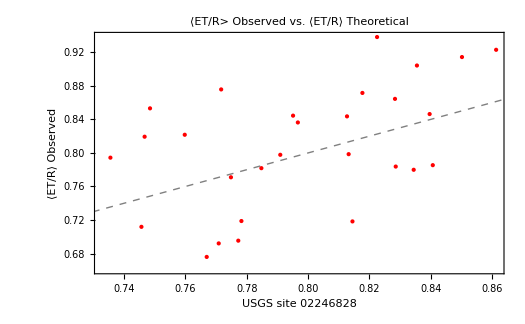

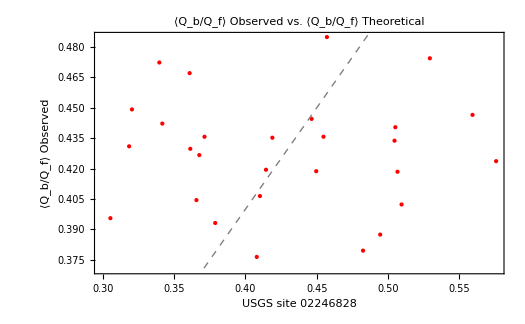

```mathematica
pairedList=Transpose[{ETRtheoretical,ETRlist }];
pairedList2=Transpose[{QbQftheoretical,QbQflist }];
(*Calculate dynamic plot ranges based on data*)
range1={Min[Flatten[pairedList]]-0.05,Max[Flatten[pairedList]]+0.05};
range2={Min[Flatten[pairedList2]]-0.05,Max[Flatten[pairedList2]]+0.05};

(*Plot the first set with dynamic 1:1 dashed gray line*)
ListPlot[pairedList,PlotStyle->{Red,PointSize[Medium]},Frame->True,FrameLabel->{Style["USGS site 02246828",Bold,14],Style["⟨ET/R⟩ Observed",Bold,14]},PlotLabel->Style["⟨ET/R> Observed vs. ⟨ET/R⟩ Theoretical",14,Bold],Epilog->{Dashed,Gray,Line[{{0,0},{1,1}}]},LabelStyle->12]

(*Plot the second set with dynamic 1:1 dashed gray line*)
ListPlot[pairedList2,PlotStyle->{Red,PointSize[Medium]},Frame->True,FrameLabel->{Style["USGS site 02246828",Bold,14],Style["⟨Q_b/Q_f⟩ Observed",Bold,14]},PlotLabel->Style["⟨Q_b/Q_f⟩ Observed vs. ⟨Q_b/Q_f⟩ Theoretical",14,Bold],Epilog->{Dashed,Gray,Line[{{0,0},{1,1}}]},PlotRange->All]
```

```mathematica
Correlation@@Transpose[pairedList]
Correlation@@Transpose[pairedList2]
```

0.494692

0.0304473

{a→0.220157,b→-0.320149}

{a→0.480408,b→-0.946034}

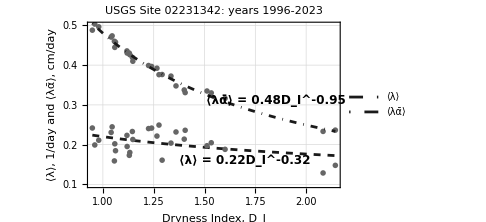

FittedModel[0.220157/x^0.320149]

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.220157 | 0.00844755 | 26.0617 | 3.66738×10^-20
b | -0.320149 | 0.14194 | -2.25553 | 0.0327422

0.980419

```mathematica
data1= Transpose[{DIlist,1/αlist 1/DIlist PETlist/10}];
data2= Transpose[{DIlist,1/DIlist PETlist/10}];

fit1=FindFit[data1,a x^b,{a,b},x]
fit2 = FindFit[data2,a x^b,{a,b},x]


(*Get parameter values for formatting*)
{a1,b1}={a,b}/. fit1;
{a2,b2}={a,b}/. fit2;

alphalambdaDI1 =Show[Plot[a x^b/. fit1,{x,Min[DIlist],Max[DIlist]},PlotStyle->{Dashed,GrayLevel[.1]},PlotRange->{Automatic,{.1,.5}},PlotLegends->Placed[{"⟨λ⟩"},{Scaled[{0.86,0.85}], {.5, 0.5}}],ImageSize->Medium,PlotTheme->"Detailed"],ListPlot[data1,PlotStyle->{GrayLevel[.4]}, PlotMarkers->Graphics[{Thickness[0.01],Circle[{0,0},Scaled[0.015]]}]],ListPlot[data2,PlotStyle->{GrayLevel[.4]},PlotMarkers->Graphics[{Style[Text["x"],FontSize->14,FontWeight->Bold]}]],Plot[{a x^b/. fit2},{x,Min[DIlist],Max[DIlist]},PlotStyle->{DotDashed,GrayLevel[.1]},PlotLegends->Placed[{"⟨λᾱ⟩"},{Scaled[{0.87,0.95}], {.5, 0.5}}]],Frame->{{True,False},{True,False}},FrameLabel->{{"⟨λ⟩, 1/day and ⟨λᾱ⟩, cm/day",None},{"Dryness Index, D_I", None}},LabelStyle->Directive[Textsize  ,Bold],PlotLabel->Style["USGS Site 0" <>ToString[selectedRow["usgs_site_no"]]<>": years 1996-2023",14,Bold],PlotRangeClipping->False,Epilog->{Text[Style[Row[{"⟨λ⟩ = ",NumberForm[a1,{3,2}],Superscript[" D_I",NumberForm[b1,{3,2}]]}],12,Bold],{1.7,0.16}],(*Adjust position if needed*)Text[Style[Row[{"⟨λᾱ⟩ = ",NumberForm[a2,{3,2}],Superscript[" D_I",NumberForm[b2,{3,2}]]}],12,Bold],{1.85,0.31}]  (*Adjust position as needed*)}]
model=NonlinearModelFit[data1,a x^b,{a,b},x]
model["ParameterTable"]
model["AdjustedRSquared"]
```

```mathematica
λwDIlist[[1]]
```

0.229929

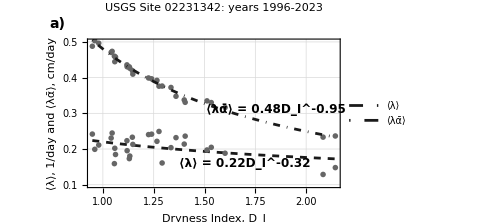

```mathematica
labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{-0.12,1.1}]]}]]

alphalambdaDI1l1 = labeledPlot[alphalambdaDI1,"a)"]
```

```mathematica
Round[DI,.01]
```

1.27

0.203836

0.382613

1.87706

74.4002

0.223942

0.505227

2.25606

0.172471

0.233524

1.35399

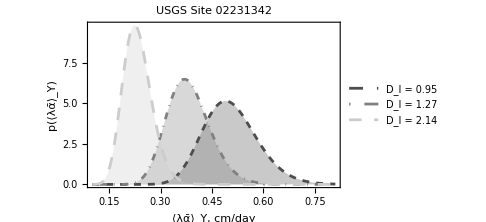

```mathematica
(*Avg Condi*)
λDI = (a DI^b)/.fit1
αλDI = ( (a DI^b)/.fit2)
αλDI/λDI
λDI 365
(*Wet Condition*)
λDIwet = (a Min[DIlist]^b)/.fit1
αλDIwet = ( (a Min[DIlist]^b)/.fit2)
αλDIwet/λDIwet
(*Dry Condition*)
λDIdry = (a Max[DIlist]^b)/.fit1
αλDIdry = ( (a Max[DIlist]^b)/.fit2)
αλDIdry/λDIdry
alphalambdaPDFs1=Plot[{VarPDF[z,λDIwet 365, (a Min[DIlist]^b)/.fit1,αλDIwet/λDIwet],VarPDF[z,λDI 365, (a DI^b)/.fit1,αλDI/λDI],VarPDF[z,λDIdry 365, (a Max[DIlist]^b)/.fit1,αλDIdry/λDIdry]},{z,.101,.81},PlotLegends->Placed[{Style["D_I = " <>ToString[Round[Min[DIlist],.01]],12], Style["D_I = "<>ToString[Round[DI,.01] ],12], Style["D_I = "<>ToString[Round[Max[DIlist],.01]],12]},{Scaled[{0.85,0.85}], {.5, 0.5}}],Frame->{{True,False},{True,False}},FrameLabel->{{"p(⟨λᾱ⟩_Y)",None},{"⟨λᾱ⟩_Y, cm/day", None}},LabelStyle->Directive[Textsize ,Bold],PlotLabel->Style["USGS Site 0" <>ToString[selectedRow["usgs_site_no"]],14,Bold],PlotRangeClipping->False, PlotStyle->{{Dashed,GrayLevel[.3]}, {DotDashed,GrayLevel[.5]},{Dashing[.025],GrayLevel[.8]}},Filling->{1->{Axis,Opacity[0.3,GrayLevel[.3]]},2->{Axis,Opacity[0.3,GrayLevel[.5]]},3->{Axis,Opacity[0.3,GrayLevel[.8]]}},ImageSize->Medium]
```

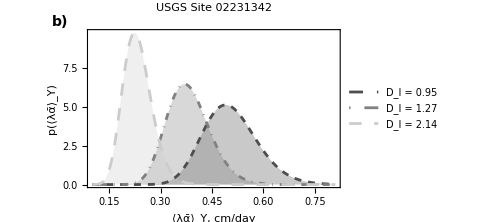

```mathematica
labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{-0.11,1.05}]]}]]
alphalambdaPDFs1l1 = labeledPlot[alphalambdaPDFs1,"b)"]
```

```mathematica
λDIdry 365
λDI 365
λDIwet 365
```

62.9519

74.4002

81.7389

```mathematica
DIlist1 = Table[DI,{DI,Range[Min[DIlist]-.075,Max[DIlist],.05]}];
λwDIlist = Table[(a DI^b)/.fit1, {DI,DIlist1} ];
nlist =365*λwDIlist;
RαλwDIlist = Table[(a DI^b)/.fit2, {DI,DIlist1} ];
αwDIlist=RαλwDIlist/λwDIlist ;
BIlist1 = Qbmax/RαλwDIlist;
```

0.281663

0.183381

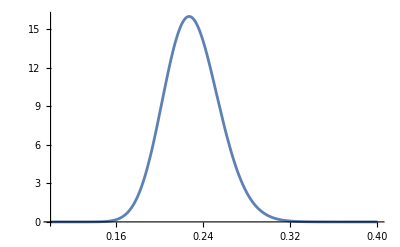

```mathematica
InverseCDF[GammaDistribution[nlist[[1]],λwDIlist[[1]]/nlist[[1]]],.975]
InverseCDF[GammaDistribution[nlist[[1]],λwDIlist[[1]]/nlist[[1]]],.025]
Plot[PDF[GammaDistribution[nlist[[1]],λwDIlist[[1]]/nlist[[1]]],λ],{λ,.1,.4}]
```

```mathematica
αλup=MapThread[VarInverseCDF[1-.025,#1,#2,#3,#4] &,{nlist ,λwDIlist,αwDIlist,RαλwDIlist }];
αλdown=MapThread[VarInverseCDF[.025,#1,#2,#3, #4] &,{nlist ,λwDIlist,αwDIlist,RαλwDIlist }];
DIlistup=(αλup/a)^(1/b)/.fit2 ;
DIlistdown = (αλdown/a)^(1/b)/.fit2 ;

αup=αλup/(a DIlistup^b/.fit1);
αdown=αλdown/(a DIlistdown^b/.fit1);
BIlistup = Qbmax/αλup;
BIlistdown = Qbmax/αλdown;
ETRtheoreticalupBounds=MapThread[ETReq,{DIlistup,BIlistup ,αup}];
ETRtheoreticaldownBounds=MapThread[ETReq,{DIlistdown,BIlistdown ,αdown}];
ETRtheoreticalBounds=MapThread[ETReq,{DIlist1,BIlist1,αwDIlist}];
QbQftheoreticalupBounds=MapThread[QbQfeq,{DIlistup,BIlistup ,αup}];
QbQftheoreticaldownBounds=MapThread[QbQfeq,{DIlistdown,BIlistdown ,αdown}];
QbQftheoreticalBounds=MapThread[QbQfeq,{DIlist1,BIlist1,αwDIlist}];
```

```mathematica
yearlist
```

{1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022,2023}

```mathematica
ETdownBound=Transpose[{ETRtheoreticalBounds,ETRtheoreticaldownBounds}];
ETupBound=Transpose[{ETRtheoreticalBounds,ETRtheoreticalupBounds}];

QbQfdownBound=Transpose[{QbQftheoreticalBounds,QbQftheoreticaldownBounds}];
QbQfupBound=Transpose[{QbQftheoreticalBounds,QbQftheoreticalupBounds}];

labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{-0.135,1.05}]]}]]
(*Plot the first set with dynamic 1:1 dashed gray line*)
ETRl1 =labeledPlot[ListPlot[{Drop[pairedList,0],ETdownBound,ETupBound},(*PlotStyle->{Red,PointSize[Medium]}*)Frame->True,PlotStyle->{{GrayLevel[.3]},(*Bold black x's for pairedList*){Gray,Thin},(*Thin gray line for ETdownBound*){Gray,Thin}},Joined->{False, True,True},Filling->{2->{3}},FillingStyle->{GrayLevel[.9]},PlotMarkers->{Graphics[{Thickness[0.01],Circle[{0,0},Scaled[0.012]]}],"",""},FrameLabel->{Style["⟨OverBar[ET]⟩/⟨R̄⟩ Theoretical",Bold,Textsize ],Style["⟨OverBar[ET]⟩/⟨R̄⟩ Observed",Bold,Textsize ]},PlotLabel->Style["USGS Site 0" <>ToString[selectedRow["usgs_site_no"]]<>": years 1996-2023",14,Bold],Epilog->{Dashed,Gray,Line[{{.69,.69},{.9,.9}}]},LabelStyle->Directive[Textsize  ,Bold],PlotRangeClipping->False,ImageSize->Medium],"a)"]

labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{-0.11,1.05}]]}]]

QbQfl1 =labeledPlot[ListPlot[{Drop[pairedList2,0],QbQfdownBound,QbQfupBound},(*PlotStyle->{Red,PointSize[Medium]}*)Frame->True,PlotStyle->{{GrayLevel[.3]},(*Bold black x's for pairedList*){Gray,Thin},(*Thin gray line for ETdownBound*){Gray,Thin}},Joined->{False, True,True},Filling->{2->{3}},FillingStyle->{GrayLevel[.9]},PlotMarkers->{Graphics[{Thickness[0.01],Circle[{0,0},Scaled[0.012]]}],"",""},FrameLabel->{Style["⟨(Q̄)_b⟩/⟨(Q̄)_f⟩ Theoretical",Bold,Textsize ],Style["⟨(Q̄)_b⟩/⟨(Q̄)_f⟩ Observed",Bold,Textsize ]},PlotLabel->Style["USGS Site 0" <>ToString[selectedRow["usgs_site_no"]]<>": years 1996-2023",14,Bold],Epilog->{Dashed,Gray,Line[{{.29,.29},{1,1}}]},LabelStyle->Directive[Textsize  ,Bold],PlotRangeClipping->False,ImageSize->Medium],"b)"]
```

-Graphics-

-Graphics-

```mathematica
PETlist
```

{4.86129,4.86129,4.86129,4.86129,4.86129,4.82809,4.83251,4.70115,4.81794,4.70687,5.07051,5.06531,4.8731,4.97195,5.06488,5.06159,4.96605,4.91775,4.88712,4.8973,4.86291,4.95199,4.64846,4.79818,4.62632,4.72684,4.72881,4.80404}

{ω→0.980946,α1→1.63911,α2→6.95211}

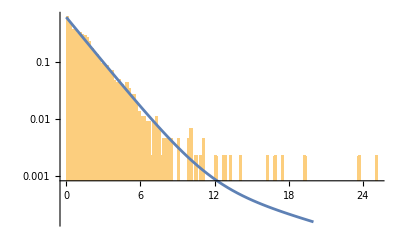

0.892367

0.688266

0.0323617

1.29379

USGS site 2235200

1.63911

6.95211

1.74035

363.544

0.1

0.00576396

0.149014

0.0568754

```mathematica
site = 35;(*25*)
eventRunoffsite = DeleteCases[eventRunoff[[All,site+1]],""];
eventRainfallsite = DeleteCases[eventRainfall[[All,site+1]],""];
selectedRow=hydroParameters[[site]];
modelselectedRow= modelParameters[[site]];
Clear[ω,α1, α2]
params  =
FindDistributionParameters[eventRainfallsite,HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]]
α=α1 ω+α2(1-ω)/.params;
prt1 = Histogram[eventRainfallsite,80,"PDF",ScalingFunctions->{"Linear","Log"},PlotRange->All];
prt2=Plot[PDF[HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]/.params,x],{x,0,20},PlotRange->{0,2},ScalingFunctions->{"Linear","Log"}] ;
Show[prt1,prt2]
EToR=selectedRow["<ET/R>"]
QboQf =selectedRow["<Qb/Qf>"]
σQ2 = selectedRow["sigmaQ^2(cm^2)"]
DI = selectedRow["DI_mean"]
Print["USGS site ",selectedRow["usgs_site_no"]]
α1=α1/.params
α2=α2/.params
ω=ω/.params;
α = α1 ω+α2(1-ω)
w = modelselectedRow["w"]
β = modelselectedRow["beta"]
μ = modelselectedRow["mu"]
BI   = modelselectedRow["BI"]
Qbmax =  modelselectedRow["BI"]*(selectedRow["alpha_all"]/10*selectedRow["lambda_all"])
```

```mathematica
(*Step 2:Find positions with year "2000"*)
positionsYear=Flatten[Position[years=StringTake[eventRainfall[[All,1]],4],Year]];
(*Step 3:Select items from the other list based on the positions*)
selectedData=Extract[eventRainfall[[All,site+1]],List/@positionsYear];

DataSite= Select[hydroParametersYear,#["usgs_site_no"]==Interpreter["Integer"][selectedRow["usgs_site_no"]] &];

ETRlist = Flatten[ Table[{selectedRowY = Select[hydroParametersYear,#["usgs_site_no"]==Interpreter["Integer"][selectedRow["usgs_site_no"]]&&#["year"]==Interpreter["Integer"][Year] &];
selectedRowY [[1]]["<ET/R>"]},{Year, DataSite[[All,2]]}]]
QbQflist = Flatten[ Table[{selectedRowY = Select[hydroParametersYear,#["usgs_site_no"]==Interpreter["Integer"][selectedRow["usgs_site_no"]]&&#["year"]==Interpreter["Integer"][Year] &];
selectedRowY [[1]]["<Qb/Qf>"]},{Year, DataSite[[All,2]]}]]
DIlist = Flatten[ Table[{selectedRowY = Select[hydroParametersYear,#["usgs_site_no"]==Interpreter["Integer"][selectedRow["usgs_site_no"]]&&#["year"]==Interpreter["Integer"][Year] &];
selectedRowY [[1]]["DI"]},{Year, DataSite[[All,2]]}]]
BIlist = Flatten[ Table[{selectedRowY = Select[hydroParametersYear,#["usgs_site_no"]==Interpreter["Integer"][selectedRow["usgs_site_no"]]&&#["year"]==Interpreter["Integer"][Year] &];
Qbmax/((selectedRowY [[1]]["rainfall(mm)"])/365/10)},{Year, DataSite[[All,2]]}]]
PETlist = Flatten[ Table[{selectedRowY = Select[hydroParametersYear,#["usgs_site_no"]==Interpreter["Integer"][selectedRow["usgs_site_no"]]&&#["year"]==Interpreter["Integer"][Year] &];
selectedRowY [[1]]["MODIS_PET(mm/day)"]},{Year, DataSite[[All,2]]}]]
αlist = Flatten[ Table[{positionsYear=Flatten[Position[years=StringTake[eventRainfall[[All,1]],4],ToString[Year]]];
selectedData=Extract[eventRainfall[[All,site+1]],List/@positionsYear];
Mean[DeleteCases[selectedData,""]]},{Year, DataSite[[All,2]]}]]
yearlist = Flatten[ Table[{selectedRowY = Select[hydroParametersYear,#["usgs_site_no"]==Interpreter["Integer"][selectedRow["usgs_site_no"]]&&#["year"]==Interpreter["Integer"][Year] &];
selectedRowY [[1]]["year"]},{Year, DataSite[[All,2]]}]]


ETReq[DI_,BI_,α_]:=DI χIavgN1[DI,(w μ)/α]+DI aPET[DI,(w μ)/α]χavg[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]]
QbQfeq[DI_,BI_,α_]:=(BI χavg[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]])/(1-DI χIavgN1[DI,(w μ)/α]-DI aPET[DI,(w μ)/α] χavg[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]])
ETRtheoretical=MapThread[ETReq,{DIlist,BIlist,αlist }]

QbQftheoretical= MapThread[QbQfeq,{DIlist,BIlist,αlist }]
```

{0.850675,0.94377,0.786511,0.925682,0.960963,0.885426,0.904113,0.830456,0.818617,0.801103,0.936846,0.981533,0.88002,0.817731,0.871544,0.964771,0.93125,0.948096,0.901631,0.864285,0.918325,0.909766,0.860983,0.902497,0.885903,0.903826,0.861687,0.938315}

{0.670498,0.561574,0.725594,0.706096,0.829891,0.646154,0.678555,0.71635,0.651586,0.70784,0.82045,0.713962,0.619445,0.660424,0.702819,0.67509,0.657763,0.730047,0.640074,0.687724,0.691124,0.663091,0.698561,0.685304,0.673939,0.681647,0.660332,0.715513}

{1.16205,1.1132,1.43554,1.35542,2.10832,1.20474,1.06391,1.20063,1.05148,1.0952,1.88639,1.52437,1.22622,1.30206,1.51278,1.48237,1.49256,1.4003,1.09824,1.37096,1.46845,1.07434,1.0403,1.12445,1.1023,1.12518,0.982426,1.22138}

{0.137974,0.134011,0.170447,0.160934,0.255224,0.146648,0.12692,0.151337,0.127832,0.132153,0.213561,0.175509,0.14489,0.15359,0.174929,0.17208,0.175918,0.160816,0.132457,0.162257,0.168467,0.126749,0.126672,0.133028,0.132513,0.13835,0.118118,0.145642}

{4.79016,4.79016,4.79016,4.79016,4.79016,4.67243,4.7676,4.5122,4.67827,4.71349,5.02382,4.93986,4.81341,4.82159,4.91857,4.89947,4.82554,4.9524,4.71569,4.80558,4.95755,4.82084,4.67092,4.80753,4.73114,4.62562,4.73052,4.76965}

{2.07665,2.0367,1.99329,1.89693,1.31189,1.79128,1.92266,1.73632,2.19408,1.86543,1.62008,1.40805,1.8,1.67698,1.57825,1.77365,1.51278,1.48899,1.77161,1.36736,1.38299,2.04164,1.74281,1.69272,1.63824,1.76411,2.03914,1.75952}

{1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022,2023}

{0.871073,0.865314,0.894585,0.891793,0.937565,0.880112,0.861467,0.878629,0.852928,0.866344,0.925483,0.916201,0.883793,0.893384,0.910674,0.903659,0.910406,0.906571,0.868768,0.906238,0.913723,0.861304,0.860574,0.875175,0.872692,0.87114,0.84427,0.883696}

{0.637672,0.628772,0.701324,0.696325,0.833231,0.676681,0.616974,0.686599,0.59729,0.635541,0.777796,0.759552,0.674727,0.702185,0.743415,0.721209,0.750708,0.730019,0.643487,0.741067,0.750028,0.609871,0.627528,0.654604,0.656018,0.657316,0.572066,0.678701}

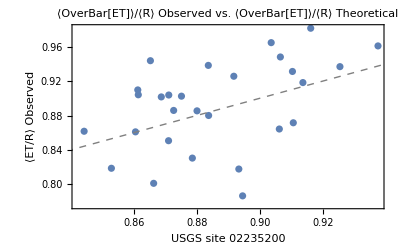

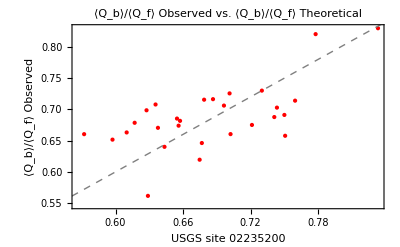

```mathematica
pairedList=Transpose[{ETRtheoretical,ETRlist }];
pairedList2=Transpose[{QbQftheoretical,QbQflist }];
(*Calculate dynamic plot ranges based on data*)
range1={Min[Flatten[pairedList]]-0.05,Max[Flatten[pairedList]]+0.05};
range2={Min[Flatten[pairedList2]]-0.05,Max[Flatten[pairedList2]]+0.05};

(*Plot the first set with dynamic 1:1 dashed gray line*)
ListPlot[{pairedList},(*PlotStyle->{Red,PointSize[Medium]}*)Frame->True,FrameLabel->{Style["USGS site 02235200",Bold,14],Style["⟨ET/R⟩ Observed",Bold,14]},PlotLabel->Style["⟨OverBar[ET]⟩/⟨R̄⟩ Observed vs. ⟨OverBar[ET]⟩/⟨R̄⟩ Theoretical",14,Bold],Epilog->{Dashed,Gray,Line[{{0,0},{1,1}}]},LabelStyle->12]
(*Plot the second set with dynamic 1:1 dashed gray line*)
ListPlot[pairedList2,PlotStyle->{Red,PointSize[Medium]},Frame->True,FrameLabel->{Style["USGS site 02235200",Bold,14],Style["⟨Q_b⟩/⟨Q_f⟩ Observed",Bold,14]},PlotLabel->Style["⟨Q_b⟩/⟨Q_f⟩ Observed vs. ⟨Q_b⟩/⟨Q_f⟩ Theoretical",14,Bold],Epilog->{Dashed,Gray,Line[{{0,0},{1,1}}]}]
```

```mathematica
Correlation@@Transpose[pairedList]
Correlation@@Transpose[pairedList2]
```

0.456423

0.632512

```mathematica
yearlist
```

{1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022,2023}

{a→0.240156,b→-0.388609}

{a→0.469522,b→-0.916514}

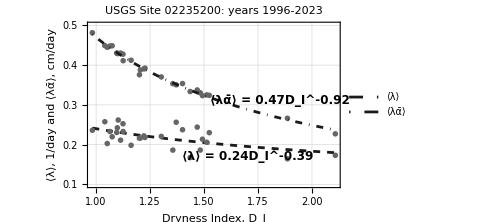

FittedModel[0.240156/x^0.388609]

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.240156 | 0.00747716 | 32.1185 | 1.87831×10^-22
b | -0.388609 | 0.11343 | -3.42599 | 0.00204603

0.98987

```mathematica
data1= Transpose[{DIlist,1/αlist 1/DIlist PETlist/10}];
data2= Transpose[{DIlist,1/DIlist PETlist/10}];

fit1=FindFit[data1,a x^b,{a,b},x]
fit2 = FindFit[data2,a x^b,{a,b},x]

(*Get parameter values for formatting*)
{a1,b1}={a,b}/. fit1;
{a2,b2}={a,b}/. fit2;

alphalambdaDI2 =Show[Plot[a x^b/. fit1,{x,Min[DIlist],Max[DIlist]},PlotStyle->{Dashed,GrayLevel[.1]},PlotRange->{Automatic,{.1,.5}},PlotLegends->Placed[{"⟨λ⟩"},{Scaled[{0.86,0.85}], {.5, 0.5}}],ImageSize->Medium,PlotTheme->"Detailed"],ListPlot[data1,PlotStyle->{GrayLevel[.4]}, PlotMarkers->Graphics[{Thickness[0.01],Circle[{0,0},Scaled[0.015]]}]],ListPlot[data2,PlotStyle->{GrayLevel[.4]},PlotMarkers->Graphics[{Style[Text["x"],FontSize->14,FontWeight->Bold]}]],Plot[{a x^b/. fit2},{x,Min[DIlist],Max[DIlist]},PlotStyle->{DotDashed,GrayLevel[.1]},PlotLegends->Placed[{"⟨λᾱ⟩"},{Scaled[{0.87,0.95}], {.5, 0.5}}]],Frame->{{True,False},{True,False}},FrameLabel->{{"⟨λ⟩, 1/day and ⟨λᾱ⟩, cm/day",None},{"Dryness Index, D_I", None}},LabelStyle->Directive[Textsize  ,Bold],PlotLabel->Style["USGS Site 0" <>ToString[selectedRow["usgs_site_no"]]<>": years 1996-2023",14,Bold],PlotRangeClipping->False,Epilog->{Text[Style[Row[{"⟨λ⟩ = ",NumberForm[a1,{3,2}],Superscript[" D_I",NumberForm[b1,{3,2}]]}],12,Bold],{1.7,0.17}],(*Adjust position if needed*)Text[Style[Row[{"⟨λᾱ⟩ = ",NumberForm[a2,{3,2}],Superscript[" D_I",NumberForm[b2,{3,2}]]}],12,Bold],{1.85,0.31}]  (*Adjust position as needed*)}]
model=NonlinearModelFit[data1,a x^b,{a,b},x]


(*Show[ListPlot[data1,PlotStyle->Red,PlotRange->All,AxesLabel->{"DIlist","y"}],Plot[a x^b/. fit1,{x,Min[DIlist],Max[DIlist]},PlotStyle->Blue],ListPlot[data2,PlotStyle->Red,PlotRange->All,AxesLabel->{"DIlist","y"}],Plot[a x^b/. fit2,{x,Min[DIlist],Max[DIlist]},PlotStyle->Blue],PlotRange->All]
model=NonlinearModelFit[data,a x^b,{a,b},x]*)
model["ParameterTable"]
model["AdjustedRSquared"]
```

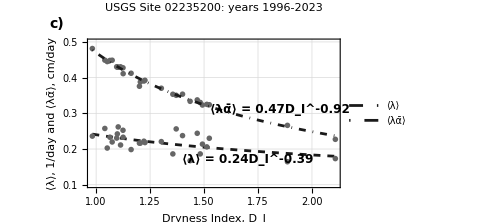

0.217281

0.370792

1.70651

79.3074

```mathematica
labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{-0.12,1.1}]]}]]
alphalambdaDI2l2 = labeledPlot[alphalambdaDI2,"c)"]
```

0.217281

0.370792

1.70651

79.3074

0.241816

0.477214

1.97346

0.179725

0.237008

1.31873

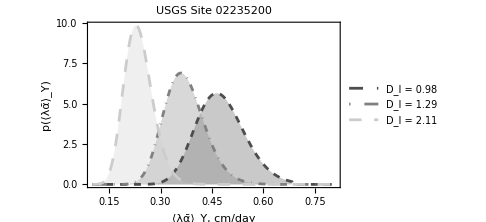

```mathematica
(*Avg Condi*)
λDI = (a DI^b)/.fit1
αλDI = ( (a DI^b)/.fit2)
αλDI/λDI
λDI 365
(*Wet Condition*)
λDIwet = (a Min[DIlist]^b)/.fit1
αλDIwet = ( (a Min[DIlist]^b)/.fit2)
αλDIwet/λDIwet
(*Dry Condition*)
λDIdry = (a Max[DIlist]^b)/.fit1
αλDIdry = ( (a Max[DIlist]^b)/.fit2)
αλDIdry/λDIdry
alphalambdaPDFs2=Plot[{VarPDF[z,λDIwet 365, (a Min[DIlist]^b)/.fit1,αλDIwet/λDIwet],VarPDF[z,λDI 365, (a DI^b)/.fit1,αλDI/λDI],VarPDF[z,λDIdry 365, (a Max[DIlist]^b)/.fit1,αλDIdry/λDIdry]},{z,.101,.81},PlotLegends->Placed[{Style["D_I = " <>ToString[Round[Min[DIlist],.01]],12], Style["D_I = "<>ToString[Round[DI,.01] ],12],Style[ "D_I = "<>ToString[Round[Max[DIlist],.01]],12]},{Scaled[{0.85,0.85}], {.5, 0.5}}],Frame->{{True,False},{True,False}},FrameLabel->{{"p(⟨λᾱ⟩_Y)",None},{"⟨λᾱ⟩_Y, cm/day", None}},LabelStyle->Directive[Textsize  ,Bold],PlotLabel->Style["USGS Site 0" <>ToString[selectedRow["usgs_site_no"]],14,Bold],PlotRangeClipping->False, PlotStyle->{{Dashed,GrayLevel[.3]}, {DotDashed,GrayLevel[.5]},{Dashing[.025],GrayLevel[.8]}},Filling->{1->{Axis,Opacity[0.3,GrayLevel[.3]]},2->{Axis,Opacity[0.3,GrayLevel[.5]]},3->{Axis,Opacity[0.3,GrayLevel[.8]]}},ImageSize->Medium]
```

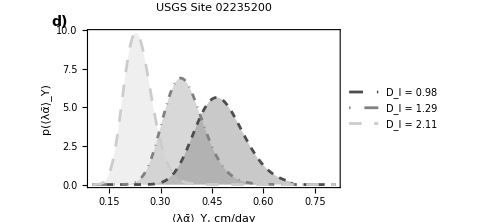

```mathematica
labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{-0.11,1.05}]]}]]
alphalambdaPDFs1l2 = labeledPlot[alphalambdaPDFs2,"d)"]
```

```mathematica
-Graphics-6
```

```mathematica
DIlist1 = Table[DI,{DI,Range[Min[DIlist]-.025,Max[DIlist]+.15,.05]}]
λwDIlist = Table[(a DI^b)/.fit1, {DI,DIlist1} ];
nlist =365*λwDIlist;
RαλwDIlist = Table[(a DI^b)/.fit2, {DI,DIlist1} ];
αwDIlist=RαλwDIlist/λwDIlist ;
BIlist1 = Qbmax/RαλwDIlist;
```

{0.957426,1.00743,1.05743,1.10743,1.15743,1.20743,1.25743,1.30743,1.35743,1.40743,1.45743,1.50743,1.55743,1.60743,1.65743,1.70743,1.75743,1.80743,1.85743,1.90743,1.95743,2.00743,2.05743,2.10743,2.15743,2.20743,2.25743}

```mathematica
αλup=MapThread[VarInverseCDF[1-.025,#1,#2,#3,#4] &,{nlist ,λwDIlist,αwDIlist,RαλwDIlist  }]
αλdown=MapThread[VarInverseCDF[.025,#1,#2,#3, #4] &,{nlist ,λwDIlist,αwDIlist ,RαλwDIlist }]
DIlistup=(αλup/a)^(1/b)/.fit2 
DIlistdown = (αλdown/a)^(1/b)/.fit2 

αup=αλup/(a DIlistup^b/.fit1)

αdown=αλdown/(a DIlistdown^b/.fit1)
BIlistup = Qbmax/αλup
BIlistdown = Qbmax/αλdown
ETRtheoreticalupBounds=MapThread[ETReq,{DIlistup,BIlistup ,αup}];
ETRtheoreticaldownBounds=MapThread[ETReq,{DIlistdown,BIlistdown ,αdown}];
ETRtheoreticalBounds=MapThread[ETReq,{DIlist1,BIlist1,αwDIlist}];
QbQftheoreticalupBounds=MapThread[QbQfeq,{DIlistup,BIlistup ,αup}];
QbQftheoreticaldownBounds=MapThread[QbQfeq,{DIlistdown,BIlistdown ,αdown}];
QbQftheoreticalBounds=MapThread[QbQfeq,{DIlist1,BIlist1,αwDIlist}];
```

{0.645093,0.617297,0.592088,0.568936,0.547507,0.527871,0.509702,0.492839,0.477142,0.462492,0.448786,0.435932,0.423853,0.412478,0.401748,0.391606,0.382005,0.372902,0.364259,0.35604,0.348214,0.340754,0.333633,0.326828,0.320319,0.314086,0.308111}

{0.358056,0.34062,0.324806,0.310398,0.29726,0.285085,0.273924,0.263606,0.254037,0.245137,0.23684,0.229086,0.221822,0.215004,0.208593,0.202551,0.196849,0.191458,0.186354,0.181514,0.176918,0.172549,0.168389,0.164424,0.16064,0.157026,0.153571}

{0.707075,0.741885,0.776415,0.81095,0.845644,0.880022,0.914304,0.948491,0.982588,1.0166,1.05052,1.08436,1.11812,1.1518,1.18541,1.21895,1.25241,1.2858,1.31913,1.35239,1.38559,1.41872,1.45179,1.4848,1.51775,1.55065,1.58348}

{1.34409,1.41933,1.49489,1.57076,1.64665,1.72353,1.80029,1.87731,1.9546,2.03215,2.10995,2.188,2.26628,2.34481,2.42356,2.50254,2.58173,2.66114,2.74077,2.82061,2.90065,2.98089,3.06133,3.14196,3.22278,3.3038,3.38499}

{2.34764,2.28883,2.23451,2.18376,2.136,2.09154,2.04976,2.01042,1.97329,1.93816,1.90486,1.87325,1.84317,1.81452,1.78718,1.76105,1.73605,1.7121,1.68913,1.66707,1.64586,1.62546,1.60581,1.58686,1.56858,1.55092,1.53386}

{1.6725,1.62509,1.5812,1.54041,1.50251,1.46675,1.4334,1.40204,1.3725,1.3446,1.31819,1.29316,1.26938,1.24676,1.2252,1.20464,1.18499,1.16619,1.14817,1.1309,1.11432,1.09838,1.08305,1.06829,1.05406,1.04034,1.02709}

{0.0881662,0.0921362,0.096059,0.099968,0.103881,0.107745,0.111586,0.115404,0.1192,0.122976,0.126732,0.130469,0.134187,0.137887,0.14157,0.145236,0.148886,0.152521,0.15614,0.159745,0.163335,0.166911,0.170473,0.174022,0.177559,0.181082,0.184594}

{0.158845,0.166976,0.175106,0.183234,0.191332,0.199503,0.207632,0.215759,0.223887,0.232014,0.240143,0.248271,0.256401,0.264531,0.272663,0.280795,0.288929,0.297064,0.305201,0.313339,0.321478,0.32962,0.337763,0.345908,0.354054,0.362203,0.370353}

```mathematica
ETdownBound=Transpose[{ETRtheoreticalBounds,ETRtheoreticaldownBounds}];
ETupBound=Transpose[{ETRtheoreticalBounds,ETRtheoreticalupBounds}];

QbQfdownBound=Transpose[{QbQftheoreticalBounds,QbQftheoreticaldownBounds}];
QbQfupBound=Transpose[{QbQftheoreticalBounds,QbQftheoreticalupBounds}];

labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{-0.135,1.05}]]}]]

(*Plot the first set with dynamic 1:1 dashed gray line*)
ETRl2 = labeledPlot[ListPlot[{Drop[pairedList,0],ETdownBound,ETupBound},(*PlotStyle->{Red,PointSize[Medium]}*)Frame->True,PlotStyle->{{Black,PointSize[Medium]},(*Bold black x's for pairedList*){Gray,Thin},(*Thin gray line for ETdownBound*){Gray,Thin}},Joined->{False, True,True},Filling->{2->{3}},FillingStyle->{GrayLevel[.9]},PlotMarkers->{Graphics[{Thickness[0.01],Circle[{0,0},Scaled[0.012]]}],"",""},FrameLabel->{Style["⟨OverBar[ET]⟩/⟨R̄⟩ Theoretical",Bold,14],Style["⟨OverBar[ET]⟩/⟨R̄⟩ Observed",Bold,14]},PlotLabel->Style["USGS Site 0" <>ToString[selectedRow["usgs_site_no"]]<>": years 1996-2023",14,Bold],Epilog->{Dashed,Gray,Line[{{.84,.84},{.94,.94}}]},LabelStyle->Directive[Textsize ,Bold],PlotRangeClipping->False,ImageSize->Medium],"c)"]

labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{-0.11,1.05}]]}]]

QbQfl2=labeledPlot[ListPlot[{Drop[pairedList2,0],QbQfdownBound,QbQfupBound},(*PlotStyle->{Red,PointSize[Medium]}*)Frame->True,PlotStyle->{{Black,PointSize[Medium]},(*Bold black x's for pairedList*){Gray,Thin},(*Thin gray line for ETdownBound*){Gray,Thin}},Joined->{False, True,True},Filling->{2->{3}},FillingStyle->{GrayLevel[.9]},PlotMarkers->{Graphics[{Thickness[0.01],Circle[{0,0},Scaled[0.012]]}],"",""},FrameLabel->{Style["⟨(Q̄)_b⟩/⟨(Q̄)_f⟩ Theoretical",Bold,14],Style["⟨(Q̄)_b⟩/⟨(Q̄)_f⟩ Observed",Bold,14]},PlotLabel->Style["USGS Site 0" <>ToString[selectedRow["usgs_site_no"]]<>": years 1996-2023",14,Bold],Epilog->{Dashed,Gray,Line[{{.56,.56},{1,1}}]},LabelStyle->Directive[Textsize ,Bold],PlotRangeClipping->False,ImageSize->Medium],"d)"]
```

-Graphics-

-Graphics-

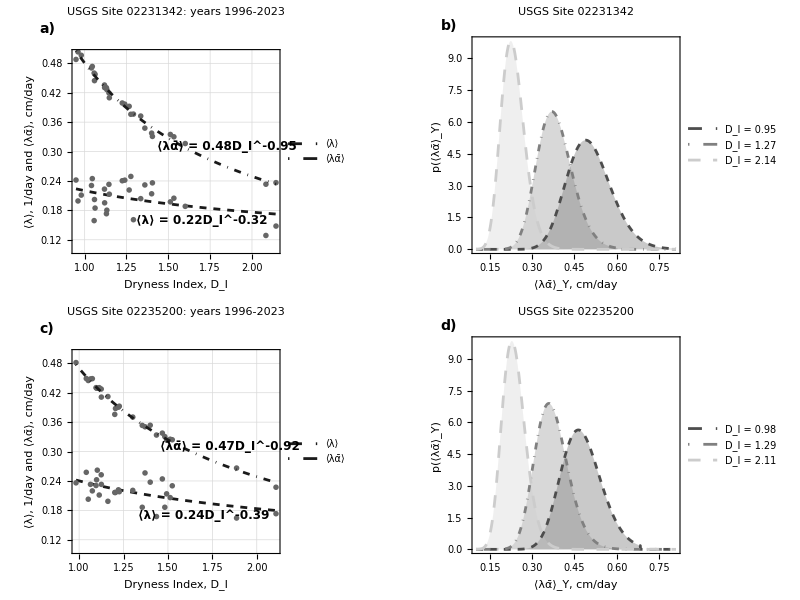

```mathematica
(*Grid with labeled figures*)
grid1=Grid[{{alphalambdaDI1l1,alphalambdaPDFs1l1},{alphalambdaDI2l2,alphalambdaPDFs1l2}},Spacings->{3,1}]
```

```mathematica
(*Grid with labeled figures*)
grid2=Grid[{{ETRl1,QbQfl1},{ETRl2,QbQfl2}},Spacings->{2,1}]
```

-Graphics-

```mathematica
Export["Figure15.eps",grid1]
```

Figure15.eps

```mathematica
Export["Figure16.eps",grid2]
```

Figure16.eps